#### Function list dump

pipe
pipeList
branch
branchSeq
deCurry
nativeSize
checkerboard
gammaDecode
gammaEncode
imgGammaDecode
imgGammaEncode
levelIndentFunc
horizontalTreeForm
GraphEdgeSleek
toRegularArray
inputHistoryViewer
StringSplitNested
colorFromHex
colorToHex
DatasetGrid
multiDimGrid
randomIntegerPartitions

```mathematica
Needs["SilviaCollection`"]
```

```mathematica
x//pipe[f,h,g]
```

g[h[f[x]]]

```mathematica
x//pipeList[f,h,g]
```

{x,f[x],h[f[x]],g[h[f[x]]]}

```mathematica
x//branch[f,h,g]
```

{f[x],h[x],g[x]}

```mathematica
x//branchSeq[f,h,g]//F
```

F[f[x],h[x],g[x]]

```mathematica
f[1,2,3,4]//deCurry
```

f[1][2][3][4]

Gamma correction is important:

```mathematica
{
ConstantImage[RGBColor[0.1725, 0.5767499999999999, 0.75],{101,101}]
,ConstantImage[RGBColor[0.88, 0.2024, 0.2024],{101,101}]
,Image[GaussianMatrix[{50,30}]//Rescale]
}//pipeList[
branch[First,pipe[Rest,Apply@SetAlphaChannel]]
,branch[Identity,Map@pipe[branchSeq[pipe[RemoveAlphaChannel,imgGammaDecode],AlphaChannel],SetAlphaChannel]]
,ImageCompose@@@#&,Map@RemoveAlphaChannel
,branch[First,pipe[Last,imgGammaEncode]]
]//pipe[
Rest,Append[{"↑ wrong blend","↑ correct blend"}]
,Grid[#,Frame->All,ItemSize->Full]&
]
```

-Graphics- | -Graphics-
{-Graphics-,-Graphics-} | {-Graphics-,-Graphics-}
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
↑ wrong blend | ↑ correct blend

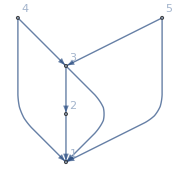

```mathematica
mygraph=Graph[{1,2,3,4,5},{2->1,3->1,3->2,4->1,4->3,5->1,5->3},VertexLabels->"Name",ImageSize->Small]
```

```mathematica
mygraph//GraphEdgeSleek
```

-Graphics-

```mathematica
RandomInteger[{0,9},4]//multiDimGrid
```

1 | 2 | 3 | 4
5 | 8 | 7 | 7

```mathematica
RandomInteger[{0,9},{2,3}]//multiDimGrid
```

| 1 | 2 | 3
1 | 9 | 2 | 0
2 | 0 | 9 | 6

```mathematica
RandomInteger[{0,9},{2,3,4}]//multiDimGrid
```

1 |  |  |  |  | 2 |  |  |  | 
 | 1 | 2 | 3 | 4 |  | 1 | 2 | 3 | 4
1 | 7 | 7 | 2 | 1 | 1 | 6 | 6 | 4 | 2
2 | 8 | 6 | 5 | 7 | 2 | 5 | 5 | 1 | 7
3 | 1 | 9 | 4 | 2 | 3 | 9 | 0 | 1 | 9

```mathematica
RandomInteger[{0,9},{2,3,4,2,1,2,3}]//multiDimGrid
```

1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 2 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 1 |  |  |  |  | 2 |  |  |  |  | 3 |  |  |  |  | 4 |  |  |  |  |  | 1 |  |  |  |  | 2 |  |  |  |  | 3 |  |  |  |  | 4 |  |  |  | 
1 |  | 1 |  |  |  |  | 1 |  |  |  |  | 1 |  |  |  |  | 1 |  |  |  | 1 |  | 1 |  |  |  |  | 1 |  |  |  |  | 1 |  |  |  |  | 1 |  |  | 
 | 1 |  | 1 | 2 | 3 | 1 |  | 1 | 2 | 3 | 1 |  | 1 | 2 | 3 | 1 |  | 1 | 2 | 3 |  | 1 |  | 1 | 2 | 3 | 1 |  | 1 | 2 | 3 | 1 |  | 1 | 2 | 3 | 1 |  | 1 | 2 | 3
 |  | 1 | 4 | 6 | 4 |  | 1 | 1 | 7 | 8 |  | 1 | 9 | 7 | 1 |  | 1 | 9 | 9 | 8 |  |  | 1 | 7 | 8 | 5 |  | 1 | 6 | 8 | 2 |  | 1 | 6 | 3 | 8 |  | 1 | 1 | 0 | 0
 |  | 2 | 6 | 5 | 6 |  | 2 | 1 | 9 | 5 |  | 2 | 5 | 9 | 8 |  | 2 | 3 | 4 | 9 |  |  | 2 | 9 | 6 | 8 |  | 2 | 9 | 8 | 0 |  | 2 | 4 | 1 | 0 |  | 2 | 9 | 5 | 2
 | 2 |  | 1 | 2 | 3 | 2 |  | 1 | 2 | 3 | 2 |  | 1 | 2 | 3 | 2 |  | 1 | 2 | 3 |  | 2 |  | 1 | 2 | 3 | 2 |  | 1 | 2 | 3 | 2 |  | 1 | 2 | 3 | 2 |  | 1 | 2 | 3
 |  | 1 | 7 | 0 | 5 |  | 1 | 3 | 6 | 8 |  | 1 | 1 | 8 | 1 |  | 1 | 7 | 6 | 1 |  |  | 1 | 5 | 7 | 1 |  | 1 | 6 | 5 | 8 |  | 1 | 8 | 3 | 9 |  | 1 | 0 | 9 | 0
 |  | 2 | 2 | 3 | 5 |  | 2 | 5 | 8 | 3 |  | 2 | 8 | 9 | 8 |  | 2 | 1 | 7 | 7 |  |  | 2 | 8 | 4 | 1 |  | 2 | 7 | 2 | 5 |  | 2 | 4 | 9 | 0 |  | 2 | 3 | 8 | 7
2 |  | 1 |  |  |  |  | 1 |  |  |  |  | 1 |  |  |  |  | 1 |  |  |  | 2 |  | 1 |  |  |  |  | 1 |  |  |  |  | 1 |  |  |  |  | 1 |  |  | 
 | 1 |  | 1 | 2 | 3 | 1 |  | 1 | 2 | 3 | 1 |  | 1 | 2 | 3 | 1 |  | 1 | 2 | 3 |  | 1 |  | 1 | 2 | 3 | 1 |  | 1 | 2 | 3 | 1 |  | 1 | 2 | 3 | 1 |  | 1 | 2 | 3
 |  | 1 | 9 | 4 | 0 |  | 1 | 0 | 0 | 0 |  | 1 | 3 | 7 | 2 |  | 1 | 7 | 7 | 2 |  |  | 1 | 5 | 2 | 3 |  | 1 | 3 | 3 | 0 |  | 1 | 2 | 5 | 4 |  | 1 | 3 | 2 | 5
 |  | 2 | 8 | 1 | 1 |  | 2 | 9 | 8 | 1 |  | 2 | 7 | 2 | 7 |  | 2 | 4 | 9 | 5 |  |  | 2 | 0 | 0 | 9 |  | 2 | 7 | 8 | 0 |  | 2 | 6 | 5 | 7 |  | 2 | 2 | 0 | 8
 | 2 |  | 1 | 2 | 3 | 2 |  | 1 | 2 | 3 | 2 |  | 1 | 2 | 3 | 2 |  | 1 | 2 | 3 |  | 2 |  | 1 | 2 | 3 | 2 |  | 1 | 2 | 3 | 2 |  | 1 | 2 | 3 | 2 |  | 1 | 2 | 3
 |  | 1 | 5 | 3 | 4 |  | 1 | 5 | 6 | 8 |  | 1 | 9 | 9 | 0 |  | 1 | 1 | 8 | 9 |  |  | 1 | 1 | 8 | 1 |  | 1 | 9 | 3 | 2 |  | 1 | 4 | 7 | 7 |  | 1 | 7 | 2 | 0
 |  | 2 | 0 | 8 | 5 |  | 2 | 6 | 9 | 9 |  | 2 | 0 | 0 | 6 |  | 2 | 1 | 4 | 0 |  |  | 2 | 2 | 3 | 2 |  | 2 | 4 | 3 | 9 |  | 2 | 5 | 5 | 5 |  | 2 | 4 | 0 | 8
3 |  | 1 |  |  |  |  | 1 |  |  |  |  | 1 |  |  |  |  | 1 |  |  |  | 3 |  | 1 |  |  |  |  | 1 |  |  |  |  | 1 |  |  |  |  | 1 |  |  | 
 | 1 |  | 1 | 2 | 3 | 1 |  | 1 | 2 | 3 | 1 |  | 1 | 2 | 3 | 1 |  | 1 | 2 | 3 |  | 1 |  | 1 | 2 | 3 | 1 |  | 1 | 2 | 3 | 1 |  | 1 | 2 | 3 | 1 |  | 1 | 2 | 3
 |  | 1 | 7 | 9 | 5 |  | 1 | 4 | 4 | 9 |  | 1 | 4 | 1 | 4 |  | 1 | 8 | 2 | 3 |  |  | 1 | 0 | 4 | 0 |  | 1 | 8 | 6 | 5 |  | 1 | 8 | 2 | 2 |  | 1 | 9 | 5 | 3
 |  | 2 | 2 | 1 | 5 |  | 2 | 7 | 6 | 3 |  | 2 | 7 | 7 | 1 |  | 2 | 3 | 0 | 8 |  |  | 2 | 6 | 5 | 0 |  | 2 | 7 | 9 | 1 |  | 2 | 6 | 4 | 8 |  | 2 | 6 | 7 | 7
 | 2 |  | 1 | 2 | 3 | 2 |  | 1 | 2 | 3 | 2 |  | 1 | 2 | 3 | 2 |  | 1 | 2 | 3 |  | 2 |  | 1 | 2 | 3 | 2 |  | 1 | 2 | 3 | 2 |  | 1 | 2 | 3 | 2 |  | 1 | 2 | 3
 |  | 1 | 1 | 4 | 7 |  | 1 | 0 | 9 | 0 |  | 1 | 4 | 2 | 9 |  | 1 | 5 | 7 | 5 |  |  | 1 | 6 | 2 | 3 |  | 1 | 2 | 2 | 1 |  | 1 | 9 | 3 | 1 |  | 1 | 4 | 9 | 2
 |  | 2 | 9 | 9 | 3 |  | 2 | 0 | 4 | 6 |  | 2 | 5 | 9 | 5 |  | 2 | 8 | 3 | 0 |  |  | 2 | 5 | 9 | 1 |  | 2 | 2 | 3 | 3 |  | 2 | 0 | 2 | 2 |  | 2 | 1 | 5 | 1

```mathematica
randomIntegerPartitions[10,5,3] // pipe[Transpose,Join[#,Thread[{" ∑ ⟹ ",Total@#}]ᵀ]&,Transpose,Grid]
```

2 | 1 | 2 | 4 | 1 |  ∑ ⟹  | 10
3 | 3 | 1 | 2 | 1 |  ∑ ⟹  | 10
2 | 2 | 2 | 2 | 2 |  ∑ ⟹  | 10